```mathematica
LambertW[0.1]//N
```

0.0912765

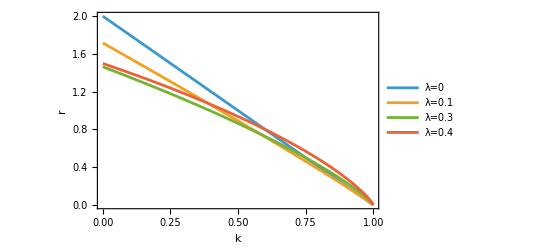

```mathematica
M=1;

Plot[Evaluate@Table[λ (1-k) LambertW[Exp[2 M/λ]/(1-k)],{λ,{10^-6,0.1,0.5,0.8}}],{k,0,1},PlotLegends->{"λ=0","λ=0.1","λ=0.3","λ=0.4"},AxesLabel->{"k","r"},Frame->True]
```

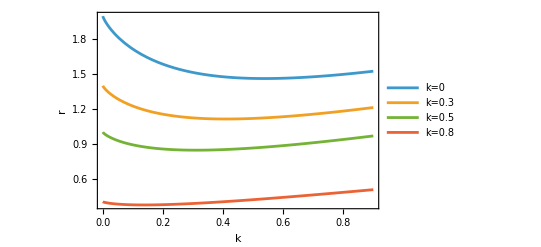

```mathematica
M=1;

Plot[Evaluate@Table[λ (1-k) LambertW[Exp[2 M/λ]/(1-k)],{k,{0,0.3,0.5,0.8}}],{λ,0,0.9},PlotLegends->{"k=0","k=0.3","k=0.5","k=0.8"},AxesLabel->{"k","r"},Frame->True]
```